### Start choosing the example:

```mathematica
t=27;
beta = 0;
A = 0.2;
(*I1=2,U1=5*)
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4,5,6,7,8,9,10},Adjacency Matrix→{{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,2}},Exit Vertices and Terminal Costs→{{10,5}},Switching Costs→{}|>

```mathematica
MFGEquations=DataToEquations[Data];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.029345,Null}

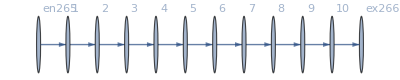

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j267→2,j268→2,j269→2,j270→2,j271→2,j272→2,j273→2,j274→2,j275→2,j276→2,j277→2,j278→0,j279→0,j280→0,j281→0,j282→0,j283→0,j284→0,j285→0,j286→0,j287→0,j288→0,jt289→0,jt290→2,jt291→2,jt292→0,jt293→2,jt294→0,jt295→2,jt296→0,jt297→2,jt298→0,jt299→2,jt300→0,jt301→2,jt302→0,jt303→2,jt304→0,jt305→2,jt306→0,jt307→2,jt308→0,u309→23,u310→21,u311→19,u312→17,u313→15,u314→13,u315→11,u316→9,u317→7,u318→5,u319→23,u320→-2+23,u321→-2+21,u322→-2+19,u323→-2+17,u324→-2+15,u325→-2+13,u326→-2+11,u327→-2+9,u328→-2+7,u329→5,u330→23|>

```mathematica
Data
```

<|Vertices List→{1,2,3,4,5,6,7,8,9,10},Adjacency Matrix→{{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,2}},Exit Vertices and Terminal Costs→{{10,5}},Switching Costs→{}|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 4.94517×10^-15

FRX1: The Error on the nonlinear terms is 4.94517×10^-15

<|j267→2,j268→2,j269→2,j270→2,j271→2,j272→2,j273→2,j274→2,j275→2,j276→2,j277→2,j278→0,j279→0,j280→0,j281→0,j282→0,j283→0,j284→0,j285→0,j286→0,j287→0,j288→0,jt289→0,jt290→2,jt291→2,jt292→0,jt293→2,jt294→0,jt295→2,jt296→0,jt297→2,jt298→0,jt299→2,jt300→0,jt301→2,jt302→0,jt303→2,jt304→0,jt305→2,jt306→0,jt307→2,jt308→0,u309→14.4188,u310→13.3722,u311→12.3257,u312→11.2792,u313→10.2327,u314→9.18612,u315→8.13959,u316→7.09306,u317→6.04653,u318→5,u319→14.4188,u320→13.3722,u321→12.3257,u322→11.2792,u323→10.2327,u324→9.18612,u325→8.13959,u326→7.09306,u327→6.04653,u328→5,u329→5,u330→14.4188|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 2.27528×10^-15

FRX1: The Error on the nonlinear terms is 2.27528×10^-15

<|j267→2,j268→2,j269→2,j270→2,j271→2,j272→2,j273→2,j274→2,j275→2,j276→2,j277→2,j278→0,j279→0,j280→0,j281→0,j282→0,j283→0,j284→0,j285→0,j286→0,j287→0,j288→0,jt289→0,jt290→2,jt291→2,jt292→0,jt293→2,jt294→0,jt295→2,jt296→0,jt297→2,jt298→0,jt299→2,jt300→0,jt301→2,jt302→0,jt303→2,jt304→0,jt305→2,jt306→0,jt307→2,jt308→0,u309→14.8916,u310→13.7925,u311→12.6935,u312→11.5944,u313→10.4953,u314→9.39627,u315→8.2972,u316→7.19814,u317→6.09907,u318→5,u319→14.8916,u320→13.7925,u321→12.6935,u322→11.5944,u323→10.4953,u324→9.39627,u325→8.2972,u326→7.19814,u327→6.09907,u328→5,u329→5,u330→14.8916|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 2.84356×10^-15

FRX1: The Error on the nonlinear terms is 2.84356×10^-15

<|j267→2,j268→2,j269→2,j270→2,j271→2,j272→2,j273→2,j274→2,j275→2,j276→2,j277→2,j278→0,j279→0,j280→0,j281→0,j282→0,j283→0,j284→0,j285→0,j286→0,j287→0,j288→0,jt289→0,jt290→2,jt291→2,jt292→0,jt293→2,jt294→0,jt295→2,jt296→0,jt297→2,jt298→0,jt299→2,jt300→0,jt301→2,jt302→0,jt303→2,jt304→0,jt305→2,jt306→0,jt307→2,jt308→0,u309→15.9945,u310→14.7729,u311→13.5513,u312→12.3297,u313→11.108,u314→9.88643,u315→8.66483,u316→7.44322,u317→6.22161,u318→5,u319→15.9945,u320→14.7729,u321→13.5513,u322→12.3297,u323→11.108,u324→9.88643,u325→8.66483,u326→7.44322,u327→6.22161,u328→5,u329→5,u330→15.9945|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

The last system in the iteration was inconsistent.
Throwing the last feasible solution.

Throw::nocatch: Uncaught Throw[<|j277→2,u329→5,j267→2,j268→2,j269→2,j270→2,j271→2,j272→2,j273→2,j274→2,j275→2,j276→2,j278→0,j279→0,j280→0,j281→0,j282→0,j283→0,j284→0,«26»,u321→-2+21,u322→-2+19,u323→-2+17,u324→-2+15,u325→-2+13,u326→-2+11,u327→-2+9,u328→-2+7,u330→23,u309→23,u310→21,u311→19,u312→17,u313→15,u314→13,u315→11,u316→9,u317→7,u319→23|>] returned to top level.

Hold[Throw[<|j277→2,u329→5,j267→2,j268→2,j269→2,j270→2,j271→2,j272→2,j273→2,j274→2,j275→2,j276→2,j278→0,j279→0,j280→0,j281→0,j282→0,j283→0,j284→0,j285→0,j286→0,j287→0,j288→0,jt289→0,jt290→2,jt291→2,jt292→0,jt293→2,jt294→0,jt295→2,jt296→0,jt297→2,jt298→0,jt299→2,jt300→0,jt301→2,jt302→0,jt303→2,jt304→0,jt305→2,jt306→0,jt307→2,jt308→0,u318→5,u320→-2+23,u321→-2+21,u322→-2+19,u323→-2+17,u324→-2+15,u325→-2+13,u326→-2+11,u327→-2+9,u328→-2+7,u330→23,u309→23,u310→21,u311→19,u312→17,u313→15,u314→13,u315→11,u316→9,u317→7,u319→23|>]]

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 6.66134×10^-15

<|j267→2,j268→2,j269→2,j270→2,j271→2,j272→2,j273→2,j274→2,j275→2,j276→2,j277→2,j278→0,j279→0,j280→0,j281→0,j282→0,j283→0,j284→0,j285→0,j286→0,j287→0,j288→0,jt289→0,jt290→2,jt291→2,jt292→0,jt293→2,jt294→0,jt295→2,jt296→0,jt297→2,jt298→0,jt299→2,jt300→0,jt301→2,jt302→0,jt303→2,jt304→0,jt305→2,jt306→0,jt307→2,jt308→0,u309→23,u310→21,u311→19,u312→17,u313→15,u314→13,u315→11,u316→9,u317→7,u318→5,u319→23,u320→21,u321→19,u322→17,u323→15,u324→13,u325→11,u326→9,u327→7,u328→5,u329→5,u330→23|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 6.42012×10^-15

FRX1: The Error on the nonlinear terms is 6.42012×10^-15

<|j267→2,j268→2,j269→2,j270→2,j271→2,j272→2,j273→2,j274→2,j275→2,j276→2,j277→2,j278→0,j279→0,j280→0,j281→0,j282→0,j283→0,j284→0,j285→0,j286→0,j287→0,j288→0,jt289→0,jt290→2,jt291→2,jt292→0,jt293→2,jt294→0,jt295→2,jt296→0,jt297→2,jt298→0,jt299→2,jt300→0,jt301→2,jt302→0,jt303→2,jt304→0,jt305→2,jt306→0,jt307→2,jt308→0,u309→26.9838,u310→24.5412,u311→22.0985,u312→19.6559,u313→17.2132,u314→14.7706,u315→12.3279,u316→9.88529,u317→7.44265,u318→5,u319→26.9838,u320→24.5412,u321→22.0985,u322→19.6559,u323→17.2132,u324→14.7706,u325→12.3279,u326→9.88529,u327→7.44265,u328→5,u329→5,u330→26.9838|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 7.85674×10^-15

FRX1: The Error on the nonlinear terms is 7.85674×10^-15

<|j267→2,j268→2,j269→2,j270→2,j271→2,j272→2,j273→2,j274→2,j275→2,j276→2,j277→2,j278→0,j279→0,j280→0,j281→0,j282→0,j283→0,j284→0,j285→0,j286→0,j287→0,j288→0,jt289→0,jt290→2,jt291→2,jt292→0,jt293→2,jt294→0,jt295→2,jt296→0,jt297→2,jt298→0,jt299→2,jt300→0,jt301→2,jt302→0,jt303→2,jt304→0,jt305→2,jt306→0,jt307→2,jt308→0,u309→37.7845,u310→34.1418,u311→30.4991,u312→26.8564,u313→23.2136,u314→19.5709,u315→15.9282,u316→12.2855,u317→8.64273,u318→5,u319→37.7845,u320→34.1418,u321→30.4991,u322→26.8564,u323→23.2136,u324→19.5709,u325→15.9282,u326→12.2855,u327→8.64273,u328→5,u329→5,u330→37.7845|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 9.10112×10^-15

FRX1: The Error on the nonlinear terms is 9.10112×10^-15

<|j267→2,j268→2,j269→2,j270→2,j271→2,j272→2,j273→2,j274→2,j275→2,j276→2,j277→2,j278→0,j279→0,j280→0,j281→0,j282→0,j283→0,j284→0,j285→0,j286→0,j287→0,j288→0,jt289→0,jt290→2,jt291→2,jt292→0,jt293→2,jt294→0,jt295→2,jt296→0,jt297→2,jt298→0,jt299→2,jt300→0,jt301→2,jt302→0,jt303→2,jt304→0,jt305→2,jt306→0,jt307→2,jt308→0,u309→44.1116,u310→39.7659,u311→35.4201,u312→31.0744,u313→26.7287,u314→22.3829,u315→18.0372,u316→13.6915,u317→9.34573,u318→5,u319→44.1116,u320→39.7659,u321→35.4201,u322→31.0744,u323→26.7287,u324→22.3829,u325→18.0372,u326→13.6915,u327→9.34573,u328→5,u329→5,u330→44.1116|>

```mathematica
alpha = 1.6001;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],200,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 6.15348×10^-15

FRX1: The Error on the nonlinear terms is 6.15348×10^-15

<|j267→2,j268→2,j269→2,j270→2,j271→2,j272→2,j273→2,j274→2,j275→2,j276→2,j277→2,j278→0,j279→0,j280→0,j281→0,j282→0,j283→0,j284→0,j285→0,j286→0,j287→0,j288→0,jt289→0,jt290→2,jt291→2,jt292→0,jt293→2,jt294→0,jt295→2,jt296→0,jt297→2,jt298→0,jt299→2,jt300→0,jt301→2,jt302→0,jt303→2,jt304→0,jt305→2,jt306→0,jt307→2,jt308→0,u309→44.1191,u310→39.7725,u311→35.426,u312→31.0794,u313→26.7328,u314→22.3863,u315→18.0397,u316→13.6931,u317→9.34657,u318→5,u319→44.1191,u320→39.7725,u321→35.426,u322→31.0794,u323→26.7328,u324→22.3863,u325→18.0397,u326→13.6931,u327→9.34657,u328→5,u329→5,u330→44.1191|>

```mathematica
alpha = 2;
FixedPoint[FixedReduceX1[MFGEquations],FFR,10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 2.86429×10^-14

FRX1: The Error on the nonlinear terms is 2.86429×10^-14

<|j267→2,j268→2,j269→2,j270→2,j271→2,j272→2,j273→2,j274→2,j275→2,j276→2,j277→2,j278→0,j279→0,j280→0,j281→0,j282→0,j283→0,j284→0,j285→0,j286→0,j287→0,j288→0,jt289→0,jt290→2,jt291→2,jt292→0,jt293→2,jt294→0,jt295→2,jt296→0,jt297→2,jt298→0,jt299→2,jt300→0,jt301→2,jt302→0,jt303→2,jt304→0,jt305→2,jt306→0,jt307→2,jt308→0,u309→152.359,u310→135.986,u311→119.612,u312→103.239,u313→86.866,u314→70.4928,u315→54.1196,u316→37.7464,u317→21.3732,u318→5,u319→152.359,u320→135.986,u321→119.612,u322→103.239,u323→86.866,u324→70.4928,u325→54.1196,u326→37.7464,u327→21.3732,u328→5,u329→5,u330→152.359|>

```mathematica
alpha = 1.605;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 9.10112×10^-15

FRX1: The Error on the nonlinear terms is 9.10112×10^-15

<|j267→2,j268→2,j269→2,j270→2,j271→2,j272→2,j273→2,j274→2,j275→2,j276→2,j277→2,j278→0,j279→0,j280→0,j281→0,j282→0,j283→0,j284→0,j285→0,j286→0,j287→0,j288→0,jt289→0,jt290→2,jt291→2,jt292→0,jt293→2,jt294→0,jt295→2,jt296→0,jt297→2,jt298→0,jt299→2,jt300→0,jt301→2,jt302→0,jt303→2,jt304→0,jt305→2,jt306→0,jt307→2,jt308→0,u309→44.4907,u310→40.1029,u311→35.715,u312→31.3271,u313→26.9393,u314→22.5514,u315→18.1636,u316→13.7757,u317→9.38786,u318→5,u319→44.4907,u320→40.1029,u321→35.715,u322→31.3271,u323→26.9393,u324→22.5514,u325→18.1636,u326→13.7757,u327→9.38786,u328→5,u329→5,u330→44.4907|>

```mathematica
alpha = 1.61;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 7.16072×10^-15

FRX1: The Error on the nonlinear terms is 7.16072×10^-15

<|j267→2,j268→2,j269→2,j270→2,j271→2,j272→2,j273→2,j274→2,j275→2,j276→2,j277→2,j278→0,j279→0,j280→0,j281→0,j282→0,j283→0,j284→0,j285→0,j286→0,j287→0,j288→0,jt289→0,jt290→2,jt291→2,jt292→0,jt293→2,jt294→0,jt295→2,jt296→0,jt297→2,jt298→0,jt299→2,jt300→0,jt301→2,jt302→0,jt303→2,jt304→0,jt305→2,jt306→0,jt307→2,jt308→0,u309→44.877,u310→40.4462,u311→36.0155,u312→31.5847,u313→27.1539,u314→22.7231,u315→18.2923,u316→13.8616,u317→9.43078,u318→5,u319→44.877,u320→40.4462,u321→36.0155,u322→31.5847,u323→27.1539,u324→22.7231,u325→18.2923,u326→13.8616,u327→9.43078,u328→5,u329→5,u330→44.877|>

```mathematica
alpha = 1.62;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j267→2,j268→2,j269→2,j270→2,j271→2,j272→2,j273→2,j274→2,j275→2,j276→2,j277→2,j278→0,j279→0,j280→0,j281→0,j282→0,j283→0,j284→0,j285→0,j286→0,j287→0,j288→0,jt289→0,jt290→2,jt291→2,jt292→0,jt293→2,jt294→0,jt295→2,jt296→0,jt297→2,jt298→0,jt299→2,jt300→0,jt301→2,jt302→0,jt303→2,jt304→0,jt305→2,jt306→0,jt307→2,jt308→0,u309→45.672,u310→41.1529,u311→36.6338,u312→32.1147,u313→27.5956,u314→23.0765,u315→18.5573,u316→14.0382,u317→9.51911,u318→5,u319→45.672,u320→41.1529,u321→36.6338,u322→32.1147,u323→27.5956,u324→23.0765,u325→18.5573,u326→14.0382,u327→9.51911,u328→5,u329→5,u330→45.672|>

```mathematica
alpha = 1.65;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 9.10112×10^-15

FRX1: The Error on the nonlinear terms is 9.10112×10^-15

<|j267→2,j268→2,j269→2,j270→2,j271→2,j272→2,j273→2,j274→2,j275→2,j276→2,j277→2,j278→0,j279→0,j280→0,j281→0,j282→0,j283→0,j284→0,j285→0,j286→0,j287→0,j288→0,jt289→0,jt290→2,jt291→2,jt292→0,jt293→2,jt294→0,jt295→2,jt296→0,jt297→2,jt298→0,jt299→2,jt300→0,jt301→2,jt302→0,jt303→2,jt304→0,jt305→2,jt306→0,jt307→2,jt308→0,u309→48.2526,u310→43.4467,u311→38.6409,u312→33.8351,u313→29.0292,u314→24.2234,u315→19.4175,u316→14.6117,u317→9.80584,u318→5,u319→48.2526,u320→43.4467,u321→38.6409,u322→33.8351,u323→29.0292,u324→24.2234,u325→19.4175,u326→14.6117,u327→9.80584,u328→5,u329→5,u330→48.2526|>

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 9.3996×10^-15

FRX1: The Error on the nonlinear terms is 9.3996×10^-15

<|j267→2,j268→2,j269→2,j270→2,j271→2,j272→2,j273→2,j274→2,j275→2,j276→2,j277→2,j278→0,j279→0,j280→0,j281→0,j282→0,j283→0,j284→0,j285→0,j286→0,j287→0,j288→0,jt289→0,jt290→2,jt291→2,jt292→0,jt293→2,jt294→0,jt295→2,jt296→0,jt297→2,jt298→0,jt299→2,jt300→0,jt301→2,jt302→0,jt303→2,jt304→0,jt305→2,jt306→0,jt307→2,jt308→0,u309→53.3351,u310→47.9645,u311→42.594,u312→37.2234,u313→31.8528,u314→26.4823,u315→21.1117,u316→15.7411,u317→10.3706,u318→5,u319→53.3351,u320→47.9645,u321→42.594,u322→37.2234,u323→31.8528,u324→26.4823,u325→21.1117,u326→15.7411,u327→10.3706,u328→5,u329→5,u330→53.3351|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.06581×10^-14

FRX1: The Error on the nonlinear terms is 1.06581×10^-14

<|j267→2,j268→2,j269→2,j270→2,j271→2,j272→2,j273→2,j274→2,j275→2,j276→2,j277→2,j278→0,j279→0,j280→0,j281→0,j282→0,j283→0,j284→0,j285→0,j286→0,j287→0,j288→0,jt289→0,jt290→2,jt291→2,jt292→0,jt293→2,jt294→0,jt295→2,jt296→0,jt297→2,jt298→0,jt299→2,jt300→0,jt301→2,jt302→0,jt303→2,jt304→0,jt305→2,jt306→0,jt307→2,jt308→0,u309→67.9182,u310→60.9273,u311→53.9364,u312→46.9455,u313→39.9546,u314→32.9637,u315→25.9727,u316→18.9818,u317→11.9909,u318→5,u319→67.9182,u320→60.9273,u321→53.9364,u322→46.9455,u323→39.9546,u324→32.9637,u325→25.9727,u326→18.9818,u327→11.9909,u328→5,u329→5,u330→67.9182|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.87992×10^-14

FRX1: The Error on the nonlinear terms is 1.87992×10^-14

<|j267→2,j268→2,j269→2,j270→2,j271→2,j272→2,j273→2,j274→2,j275→2,j276→2,j277→2,j278→0,j279→0,j280→0,j281→0,j282→0,j283→0,j284→0,j285→0,j286→0,j287→0,j288→0,jt289→0,jt290→2,jt291→2,jt292→0,jt293→2,jt294→0,jt295→2,jt296→0,jt297→2,jt298→0,jt299→2,jt300→0,jt301→2,jt302→0,jt303→2,jt304→0,jt305→2,jt306→0,jt307→2,jt308→0,u309→94.0472,u310→84.153,u311→74.2589,u312→64.3648,u313→54.4707,u314→44.5765,u315→34.6824,u316→24.7883,u317→14.8941,u318→5,u319→94.0472,u320→84.153,u321→74.2589,u322→64.3648,u323→54.4707,u324→44.5765,u325→34.6824,u326→24.7883,u327→14.8941,u328→5,u329→5,u330→94.0472|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 2.86429×10^-14

FRX1: The Error on the nonlinear terms is 2.86429×10^-14

<|j267→2,j268→2,j269→2,j270→2,j271→2,j272→2,j273→2,j274→2,j275→2,j276→2,j277→2,j278→0,j279→0,j280→0,j281→0,j282→0,j283→0,j284→0,j285→0,j286→0,j287→0,j288→0,jt289→0,jt290→2,jt291→2,jt292→0,jt293→2,jt294→0,jt295→2,jt296→0,jt297→2,jt298→0,jt299→2,jt300→0,jt301→2,jt302→0,jt303→2,jt304→0,jt305→2,jt306→0,jt307→2,jt308→0,u309→152.359,u310→135.986,u311→119.612,u312→103.239,u313→86.866,u314→70.4928,u315→54.1196,u316→37.7464,u317→21.3732,u318→5,u319→152.359,u320→135.986,u321→119.612,u322→103.239,u323→86.866,u324→70.4928,u325→54.1196,u326→37.7464,u327→21.3732,u328→5,u329→5,u330→152.359|>

### What we this plot for?

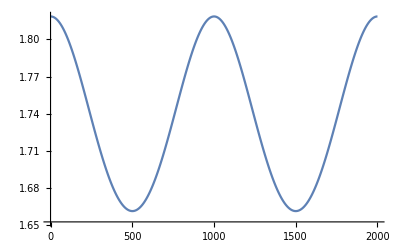

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.